This is a version of the angle code, cleaned up for production, and encapsulated inside a Module, which is a Mathematica version of a function. The name of this function is Submerged, and it takes one input which is the angle “theta”. It uses the := construction which delays the evaluation of this function until it is actually called. All the lines of the function end in a semi-colon, except for the last one which is the only quantity returned from the function. If you wanted to return multiple quantities you would use a list. Note that we’ve just defined the mass and a center of mass for convenience - you should edit this. Also, we’ve used a couple of built-in Mathematica functions, including RegionMeasure and RegionCentroid - you don’t have to use these but they are convenient.

```mathematica
Submerged[theta_]:=Module[{},
boat = ImplicitRegion[x^2/2<y<2,{{x,-2,2},{y,-2,2}}];
water = ImplicitRegion[If[theta<90,y<Tan[theta Degree]*x+d,y>Tan[theta Degree]*x+d],{{x,-2,2},{y,-2,2}}];
mass = 21000;
com = {0,0.91428571428571,0};
under = RegionIntersection[boat,water];
disp = 1000*10*RegionMeasure[under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = Append[RegionCentroid[under/.{d->draft}],0];
buoyancy = mass*98/10*{-Sin[theta Degree],Cos[theta Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque
]
```

Here we test the function, which is supposed to return the torque, for different angles. Remember that it won’t work with angles at 90 or very close to 90.

```mathematica
Submerged[91]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

67306.8

Now we generate the stability curve, but calling the function for a bunch of different angle values - Mathematica uses Table to achieve this. Notice that we’ve defined the angles here, and we’ve skipped over the angles from 80 to 100.

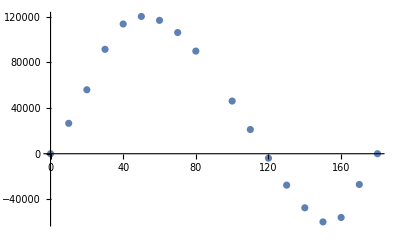

```mathematica
ListPlot[Table[{theta,Submerged[theta]},{theta,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}]]
```